```mathematica
SetDirectory[NotebookDirectory[]];
Import["init.wl"];
```

```mathematica
tcheby[npts_,xmin_,xmax_]:=Module[{pts,fb,del},del=xmax-xmin;pts=N[Table[(i del)/(npts+1)+xmin,{i,npts}]];fbrke=N[Table[((i π)/del)^2,{i,npts}]];w=N[Table[del/(npts+1),{i,npts}]];T=N[Table[√(2./(npts+1)) Sin[((i j) π)/(npts+1)],{i,npts},{j,npts}]];Return[{pts,T,fbrke,w}]]
dv2fb[DVR_,T_]:=T.DVR.Transpose[T];
fb2dv[FBR_,T_]:=Transpose[T].FBR.T;
```

```mathematica
npts = 100 ; 
xmin = -3.0;
xmax = +32.0;
De = 3.0;
a = .5 ; 
m = 1.0; 
ℏ  = 1.0; 
{pts,T,fbrke,w} = tcheby[npts,xmin,xmax];
V[x_]:= De ( 1- Exp[- a x])^2-De;
Vdvr = V[pts]//Thread;
fbrke = fbrke * ℏ^2/(2m);
Hdvr =  fb2dv[DiagonalMatrix[fbrke],T] + DiagonalMatrix[Vdvr];
```

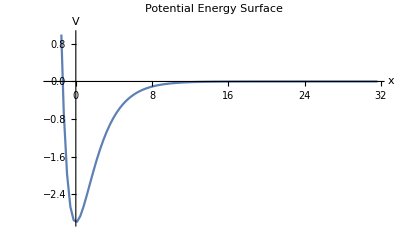

```mathematica
plotV=ListPlot[Transpose[{pts,Vdvr}],PlotRange->{-3,1},Joined->True,AxesLabel->{"x","V"},PlotLabel->"Potential Energy Surface"]
```

```mathematica
{ω,ϕ}=Transpose[Sort[Transpose[Eigensystem[Hdvr]]]];
```

```mathematica
TableForm[Take[ω,10]]
```

-2.41888
-1.44413
-0.719388
-0.244643
-0.0198923
0.0113421
0.0400867
0.0823905
0.136925
0.202919

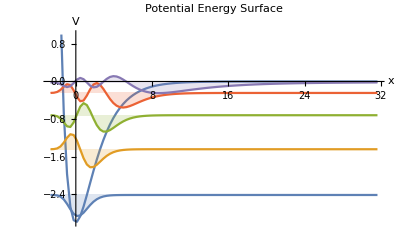

```mathematica
pltWF = ListPlot[Table[Transpose[{pts,ω[[i]]+ϕ[[i]]}],{i,1,5}],PlotRange->{{-3,32},{-3,1}},Joined->True,
Filling->Table[i->ω[[i]],{i,1,5}]];
Show[plotV,pltWF]
```

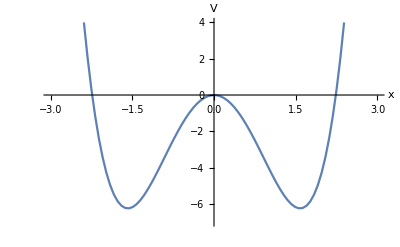

```mathematica
{pts2,T2,fbrke2,w2}=tcheby[100,-3.5,3.5];
V2[x_]:=-5 x^2+x^4;
Vdvr2=Thread[V2[pts2]];
m=1.;
pltV = ListPlot[Transpose[{pts2,Vdvr2}],PlotRange->{{-3,3},{-7,4}},Joined->True,AxesLabel->{"x","V"}]
fbrke2=fbrke2/(2 m);Hdvr=fb2dv[DiagonalMatrix[fbrke2],T2]+DiagonalMatrix[Vdvr2];{ω,ψ}=Transpose[Sort[Transpose[Eigensystem[Hdvr]]]];
```

```mathematica
TableForm[Take[ω,10]]
```

-4.13576
-4.11911
-0.756761
-0.210676
1.92129
3.8373
6.18057
8.7403
11.5102
14.4645

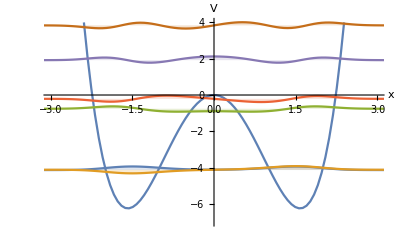

```mathematica
nn = 10;
pltWF = ListPlot[Table[Transpose[{pts2,ω[[i]]+ψ[[i]]}],{i,1,nn}],Joined->True,
Filling->Table[i->ω[[i]],{i,1,nn}]];
Show[pltV,pltWF]
```

```mathematica
npts = 25;
xmin = -3.5;
xmax = 3.5;
params = {A-> 1,B-> -5,xo-> 1.5,β-> 0.5,ℏ-> 1,δt-> 0.1,m-> 1};

V[x_]:=-5 x^2+x^4;

tcheby[npts_,xmin_,xmax_]:=Module[{pts,fb,del},del=xmax-xmin;
pts=Table[i*del*(1/(npts+1))+xmin,{i,npts}]//N;
fbrke=Table[(i*(Pi/del))^2,{i,npts}]//N;
w=Table[del/(npts+1),{i,npts}]//N;
T=Table[Sqrt[2.0/(npts+1)]*Sin[(i*j)*Pi/(npts+1)],{i,npts},{j,npts}]//N;
Return[{pts,T,fbrke,w}];]

{pts,T,fbrke,w}=tcheby[npts,xmin,xmax];

fbrke = fbrke/(2 m);

ExpV =(Exp[-ⅈ V[pts] δt/ℏ]/.params)//Thread;
ExpK = (Exp[-ⅈ/ℏ fbrke δt/2]/.params)//Thread;
TT = Transpose[T];

UK = T.DiagonalMatrix[ExpK].TT;
U = UK.DiagonalMatrix[ExpV].UK;
```

```mathematica
ψo[x_]:=(β/π)^(1/4) ⅇ^(-β (x-xo)^2);ϕo=Thread[ψo[pts]/.params]; 
norm=√(ϕo.ϕo);ϕo=ϕo/norm; ψt={ϕo}; ct={1};evolve={ListPlot[Transpose[{pts,ϕo}],Joined->True,DisplayFunction->Identity]};
nsteps=25000;
 ϕt=ϕo;
 Do[ϕt=U.ϕt;c=ϕo.ϕt;ct=Append[ct,c];If[Mod[n,1000]==0,ψt=Append[ψt,ϕt];pp=ListPlot[Transpose[{pts,Abs[ϕt]}],Joined->True,DisplayFunction->Identity];evolve=Append[evolve,pp]],{n,nsteps}]; ct1=ct;
```

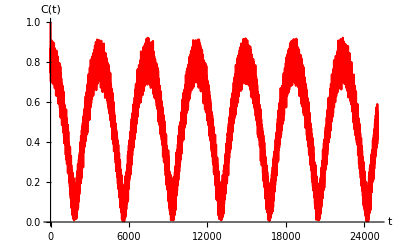

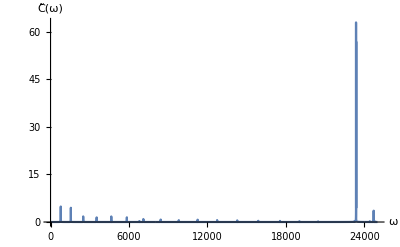

```mathematica
correl1=ListPlot[Abs[ct1],Joined->True,PlotStyle->RGBColor[1,0,0],AxesLabel->{"t","C(t)"}]
cft1=Fourier[ct];
ct1plot=ListPlot[Abs[cft1],PlotRange->All,Joined->True,AxesLabel->{"ω","\!\(\*OverscriptBox[\(C\), \(~\)]\)(ω)"}]
```

```mathematica
ListPlot[Transpose[{pts,-(ψ⟦1⟧+ψ⟦2⟧)/(√2)}],Joined->True]
ϕo=-(ψ⟦1⟧+ψ⟦2⟧)/(√2);
ψt={ϕo};
ct={1};
evolve={ListPlot[Transpose[{pts,ϕo}],Joined->True,DisplayFunction->Identity]};
nsteps=25000;
ϕt=ϕo;
Do[ϕt=U.ϕt;c=ϕo.ϕt;ct=Append[ct,c];If[Mod[n,10000]==0,ψt=Append[ψt,ϕt];pp=ListPlot[Transpose[{pts,Abs[ϕt]}],Joined->True,DisplayFunction->Identity];evolve=Append[evolve,pp]],{n,nsteps}];
ct2=ct;
```

Transpose::nmtx: The first two levels of {{-3.23077,-2.96154,-2.69231,-2.42308,-2.15385,-1.88462,-1.61538,«12»,1.88462,2.15385,2.42308,2.69231,2.96154,3.23077},{«23»,«49»,«50»}} cannot be transposed.

ListPlot::lpn: Transpose[{{-3.23077,-2.96154,-2.69231,-2.42308,-2.15385,-1.88462,-1.61538,«12»,1.88462,2.15385,2.42308,2.69231,2.96154,3.23077},{«1»}}] is not a list of numbers or pairs of numbers.

ListPlot[Transpose[{{-3.23077,-2.96154,-2.69231,-2.42308,-2.15385,-1.88462,-1.61538,-1.34615,-1.07692,-0.807692,-0.538462,-0.269231,0.,0.269231,0.538462,0.807692,1.07692,1.34615,1.61538,1.88462,2.15385,2.42308,2.69231,2.96154,3.23077},{2.68424×10^-8,7.59465×10^-8,1.81563×10^-7,4.07246×10^-7,8.71183×10^-7,1.7839×10^-6,3.50164×10^-6,6.59556×10^-6,0.000011932,0.0000207511,0.0000347232,0.0000559529,0.0000868997,0.000130187,0.000188289,0.000263102,0.000355461,0.000464652,0.000588045,0.000720907,0.000856506,0.000986493,0.00110157,0.00119234,0.00125022,0.00126828,0.00124189,0.00116904,0.00105038,0.000888862,0.000689205,0.000457126,0.00019854,-0.0000812326,-0.000378163,-0.000690088,-0.00101714,-0.0013621,-0.0017306,-0.00213143,-0.00257676,-0.00308252,-0.00366893,-0.00436112,-0.00519008,-0.00619369,-0.0074181,-0.00891916,-0.010764,-0.0130329,-0.0158204,-0.0192366,-0.0234078,-0.0284755,-0.034594,-0.0419264,-0.0506368,-0.0608799,-0.0727863,-0.0864447,-0.10188,-0.119028,-0.137714,-0.157629,-0.178313,-0.199153,-0.219387,-0.238138,-0.254454,-0.267379,-0.27603,-0.279688,-0.277879,-0.270447,-0.25759,-0.239873,-0.21818,-0.193649,-0.167557,-0.141202,-0.11578,-0.0922828,-0.0714319,-0.053645,-0.0390498,-0.0275261,-0.0187713,-0.0123723,-0.00787416,-0.00483435,-0.00286049,-0.00162967,-0.000893095,-0.000470352,-0.000237822,-0.000115325,-0.0000535545,-0.0000237302,-9.87218×10^-6,-3.47479×10^-6}}],Joined→True]

Transpose::nmtx: The first two levels of {{-3.23077,-2.96154,-2.69231,-2.42308,-2.15385,-1.88462,-1.61538,«12»,1.88462,2.15385,2.42308,2.69231,2.96154,3.23077},{«23»,«49»,«50»}} cannot be transposed.

ListPlot::lpn: Transpose[{{-3.23077,-2.96154,-2.69231,-2.42308,-2.15385,-1.88462,-1.61538,«12»,1.88462,2.15385,2.42308,2.69231,2.96154,3.23077},{«1»}}] is not a list of numbers or pairs of numbers.

Dot::dotsh: Tensors {{-0.031814-0.850043 ⅈ,0.234321+0.399686 ⅈ,-0.196319-0.087358 ⅈ,«20»,0.000277561-0.000157053 ⅈ,-0.0000789106+0.000183584 ⅈ},«23»,{«1»}} and {2.68424×10^-8,7.59465×10^-8,1.81563×10^-7,4.07246×10^-7,8.71183×10^-7,1.7839×10^-6,«39»,-0.00619369,-0.0074181,-0.00891916,-0.010764,-0.0130329,«50»} have incompatible shapes.

Dot::dotsh: Tensors {2.68424×10^-8,7.59465×10^-8,1.81563×10^-7,4.07246×10^-7,8.71183×10^-7,1.7839×10^-6,«39»,-0.00619369,-0.0074181,-0.00891916,-0.010764,-0.0130329,«50»} and {{-0.031814-0.850043 ⅈ,0.234321+0.399686 ⅈ,-0.196319-0.087358 ⅈ,«20»,0.000277561-0.000157053 ⅈ,-0.0000789106+0.000183584 ⅈ},«23»,{«1»}} have incompatible shapes.

Dot::dotsh: Tensors {{-0.031814-0.850043 ⅈ,0.234321+0.399686 ⅈ,-0.196319-0.087358 ⅈ,«20»,0.000277561-0.000157053 ⅈ,-0.0000789106+0.000183584 ⅈ},«23»,{«1»}} and {2.68424×10^-8,7.59465×10^-8,1.81563×10^-7,4.07246×10^-7,8.71183×10^-7,1.7839×10^-6,«39»,-0.00619369,-0.0074181,-0.00891916,-0.010764,-0.0130329,«50»} have incompatible shapes.

General::stop: Further output of Dot::dotsh will be suppressed during this calculation.

Transpose::nmtx: The first two levels of {{-3.23077,-2.96154,-2.69231,-2.42308,-2.15385,-1.88462,-1.61538,«12»,1.88462,2.15385,2.42308,2.69231,2.96154,3.23077},Abs[{«1»}.{«1»}]} cannot be transposed.

ListPlot::lpn: Transpose[{{-3.23077,-2.96154,-2.69231,-2.42308,-2.15385,-1.88462,-1.61538,«12»,1.88462,2.15385,2.42308,2.69231,2.96154,3.23077},Abs[«1»]}] is not a list of numbers or pairs of numbers.

Transpose::nmtx: The first two levels of {{-3.23077,-2.96154,-2.69231,-2.42308,-2.15385,-1.88462,-1.61538,«12»,1.88462,2.15385,2.42308,2.69231,2.96154,3.23077},Abs[{«1»}.{«1»}]} cannot be transposed.

ListPlot::lpn: Transpose[{{-3.23077,-2.96154,-2.69231,-2.42308,-2.15385,-1.88462,-1.61538,«12»,1.88462,2.15385,2.42308,2.69231,2.96154,3.23077},Abs[«1»]}] is not a list of numbers or pairs of numbers.